```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar\\runs2"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/daq-tools-bkg-auto/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metaStructure2={Number,Number,Number,Number,Number,Number,Number,Word,Real};
metaStructure3={Real,Real,Real,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desc3.dat"],metaStructure2];
metalvl3={Real,Real,Real,Real,Real,Real,Real,Real};
ts={35,50,65,80,95,110,125,140,155,170,180,200,215,220,230,240,245,260,275,280,290,300,305,320,335,340,350,360,365,380};
tssz=Dimensions[ts][[1]];
tsadd=PlusMinus[11.3,0.397];
(*Print["Executing: ts = ",ts[[i]]," , i = ",i];*)
tfal=ReadList[StringJoin[descDir,seperator,"tf-Al.dat"],metaStructure3];
tfcu=ReadList[StringJoin[descDir,seperator,"tf-Cu.dat"],metaStructure3];
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\runs2

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

```mathematica
pttfmual=Table[{{tfal[[k]][[1]],2tsadd[[2]]},{tfal[[k]][[2]],tfal[[k]][[4]]}},{k,1,tssz}];
pttfmucu=Table[{{tfcu[[k]][[1]],2tsadd[[2]]},{tfcu[[k]][[2]],tfcu[[k]][[4]]}},{k,1,tssz}];
pttf2mual=Table[{{tfal[[k]][[1]],2tsadd[[2]]},{tfal[[k]][[5]],tfal[[k]][[7]]}},{k,1,tssz}];
pttf2mucu=Table[{{tfcu[[k]][[1]],2tsadd[[2]]},{tfcu[[k]][[5]],tfcu[[k]][[7]]}},{k,1,tssz}];
EDAListPlot[pttfmual,pttfmucu,Joined->True,Frame->True,FrameLabel->{"t_s(s)","⟨OverBar[t_f]⟩ ± σ(s)"},PlotRange->{{35,420},{0.04,0.09}},PlotLegends->{"Al","Cu"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic,Medium}]
EDAListPlot[pttf2mual,pttf2mucu,Joined->True,Frame->True,FrameLabel->{"t_s(s)","OverBar[⟨SubsuperscriptBox[t, f, 2]⟩/⟨SubscriptBox[t, f]⟩] ± σ(s)"},PlotRange->{{35,420},{0.07,0.13}},PlotLegends->{"Al","Cu"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic,Medium}]
```

-Graphics-

-Graphics-

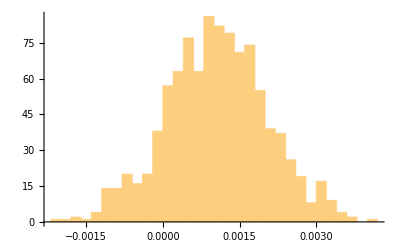

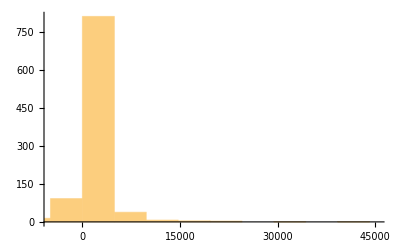

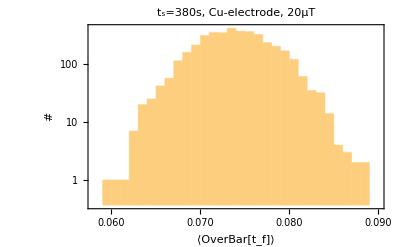

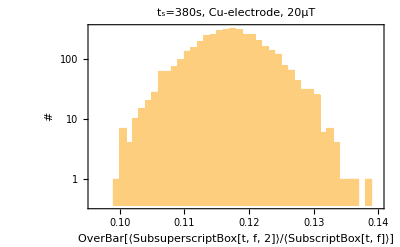

```mathematica
i=16;
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
maxsz=4000;
maxsz3=1000;
maxsz2=100000;
tf=Table[0,{k,1,maxsz}];
tf2tf=Table[0,{k,1,maxsz}];
If[i≤15,
kk=Position[tfal,descdat[[i]][[7]]+2*tsadd[[1]]][[1]][[1]];
tf=RandomVariate[NormalDistribution[tfal[[kk]][[2]],tfal[[kk]][[4]]],maxsz];
tf2tf=RandomVariate[NormalDistribution[tfal[[kk]][[5]],tfal[[kk]][[7]]],maxsz];
,
kk=Position[tfcu,descdat[[i]][[7]]+2*tsadd[[1]]][[1]][[1]];
tf=RandomVariate[NormalDistribution[tfcu[[kk]][[2]],tfcu[[kk]][[4]]],maxsz];
tf2tf=RandomVariate[NormalDistribution[tfcu[[kk]][[5]],tfcu[[kk]][[7]]],maxsz];
];
(***)
ab=RandomVariate[NormalDistribution[lvl3[[1]][[1]],lvl3[[1]][[2]]],maxsz3];
eb=RandomVariate[NormalDistribution[lvl3[[1]][[3]],lvl3[[1]][[4]]],maxsz3];
(*eb=RandomVariate[NormalDistribution[.0004,.00001],maxsz3];*)
tftseb0=Flatten[KroneckerProduct[1/eb,(descdat[[i]][[7]]+2tsadd[[1]])*tf2tf]];
tftsab=Flatten[KroneckerProduct[1/ab,(descdat[[i]][[7]]+2tsadd[[1]])/tf]];
tftseb=Flatten[KroneckerProduct[1/eb,(descdat[[i]][[7]]+2tsadd[[1]])/tf]];
Histogram[eb,PlotRange->Full]
Histogram[1/eb]
Histogram[tf,{.058,.09,.001},PlotRange->{{.058,.09},Automatic},Frame->True,FrameLabel->{"⟨OverBar[t_f]⟩","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
Histogram[tf2tf,{.096,.14,.001},PlotRange->{Automatic,Automatic},Frame->True,FrameLabel->{"OverBar[⟨SubsuperscriptBox[t, f, 2]⟩/⟨SubscriptBox[t, f]⟩] ","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
(*Histogram[Sqrt[tftseb0]]
Histogram[Sqrt[tftsab]]
Histogram[Sqrt[tftseb]]*)
```

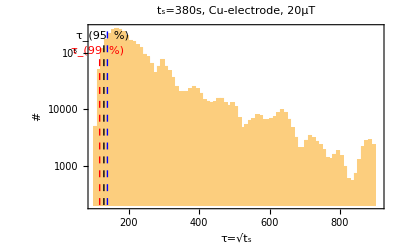

```mathematica
tk2[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[Table[{10^j,Superscript["10",j],{a,b}},{j,l,u,int}]~Join~Table[{10^j,"",{c,d}},{j,l+int/2,u-int/2,int}]],3];
endpt=10000;
(*Histogram[{Sqrt[tftsab],Sqrt[tftseb]},{100,endpt,10},PlotRange->{{100,endpt},Automatic},ChartLegends->{"√(t_s/A_B)","√(t_s/((1 - SubscriptBox[E, B])·SubscriptBox[t, f]))"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],None},{LinTicks,None}},Frame->True,FrameLabel->{"τ/f(η)","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]*)
lineStyle1={Thick,Dashed,Blue};
lineStyle2={Thick,Dashed,Black};
lineStyle3={Thick,Dashed,Red};
line1=Line[{{139,Log@(10^2.3)},{139,Log@(10^5.5)}}];
line2=Line[{{129,Log@(10^2.3)},{129,Log@(10^5.25)}}];
line3=Line[{{117,Log@(10^2.3)},{117,Log@(10^5)}}];
Histogram[Sqrt[tftseb0],{100,endpt/11,10},PlotRange->{{100,endpt/11},Automatic},Frame->True,FrameLabel->{"τ=√t_s","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT",
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{134,Log@(10^5.55)}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{124,Log@(10^5.3)}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{110,Log@(10^5.05)}],Large]}
}]
```

139.7

129.6

117.5

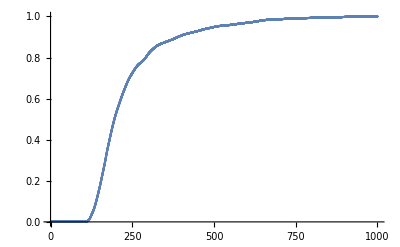

```mathematica
histtftseb0=HistogramList[Sqrt[tftseb0],{0,1000,.1}];
histtftseb0t=Transpose[{(histtftseb0[[1]][[;;-2]]+(histtftseb0[[1]][[2]]-histtftseb0[[1]][[2]])/2),histtftseb0[[2]][[;;]]}];
histhisttftseb0tot=Total[histtftseb0t[[;;,2]]];
cumhisttftseb0t=ParallelTable[{histtftseb0t[[k]][[1]],Total[histtftseb0t[[;;k,2]]]/histhisttftseb0tot},{k,1,Dimensions[histtftseb0t][[1]]}];
val90=Nearest[cumhisttftseb0t[[;;,2]],0.1][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val90]][[1]]]][[1]]
val95=Nearest[cumhisttftseb0t[[;;,2]],0.05][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val95]][[1]]]][[1]]
val99=Nearest[cumhisttftseb0t[[;;,2]],0.01][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val99]][[1]]]][[1]]
ListPlot[cumhisttftseb0t,PlotRange->{{0,1000},{0,1}}]
```

```mathematica
val=Nearest[cumhisttftseb0t[[;;,2]],0.1][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val]][[1]]]][[1]]
Sqrt[pttfmucu[[-1]][[2]][[1]]*pttfmucu[[-1]][[1]][[1]]/.00100883]
```

139.5

171.742

```mathematica
pttfmucu[[-1]]
```

{{402.6,0.794},{0.0739093,0.0040155}}